## Učni list - Kvadratna funkcija

28. Izračunaj presečišče parabole in premice:
a)	 y = -1/3x^2 - 2x - 3
	 y = -x  -  9

```mathematica
Solve[{y ==-1/3 x^2 - 2 x - 3 , y == -x - 9 }, {x, y}]
```

{{x→-6,y→-3},{x→3,y→-12}}

Odgovor: Presečišči sta P(-6, -3) in Q(3, -12).

b)	 y = 6x^2 +  x  -  1
	 y = -11x  -  7

```mathematica
Solve[{y == 6x^2 + x - 1, y == -11x - 7},{x, y}]
```

{{x→-1,y→4}}

Odgovor: Presečišče je P(-1, 4).

c)	 y = 1/2x^2 +  3x  +  4
	 y = 2x  + 8

```mathematica
Solve[{y == 1/2 x ^2 + 3x + 4, y == 2x + 8},{x, y}]
```

{{x→-4,y→0},{x→2,y→12}}

Odgovor: Presečišči sta P(-4, 0) in Q(2, 12).

d)	 y = 5 + 4 x  -  x^2
	 3x - 2y = -7

```mathematica
Solve[{y == 5+ 4x - x^2, y== (-7 - 3x) / (-2) },{x, y}]
```

{{x→-1/2,y→11/4},{x→3,y→8}}

Odgovor: Presečišči sta P(-1/2, 11/4) in Q(3, 8).

## Učni list - Potence

12. Izračunaj:
a)	 16 × 2^(-3) - 2^0 ((1,2)^2-(0,8)^2) = ?

```mathematica
Simplify[16×2^(-3)-2^0 ×((1.2)^2-(0.8)^2)]
```

1.2

Odgovor: 16 × 2^(-3) - 2^0 ((1,2)^2-(0,8)^2) =  1,2

b)	 (-8)^3 × 2 ^(-5) - 9 ^2 × ((-7)^0 - 3^(-3)) = ?

```mathematica
Simplify[(-8)^3×2^(-5)-9^2×((-7)^0-3^(-3))]
```

-94

Odgovor: (-8)^3 × 2 ^(-5) - 9 ^2 × ((-7)^0 - 3^(-3)) =  -94

c)	 (0.2)^3 × 10 ^4 - (0.125)^(-2) = ?

```mathematica
Simplify[(0.2)^3×10^4-(0.125)^(-2)]
```

16.

Odgovor: (0.2)^3 × 10 ^4 - (0.125)^(-2) =  16

d)	 (0.6)^(-2) × 0.63 - (0.75)^2 × (2 1/4)^(-1) =  ?

```mathematica
Simplify[(0.6)^(-2)×0.63-(0.75)^2×(2 1/4)^(-1)]
```

0.625

Odgovor: (0.6)^(-2)×0.63-(0.75)^2×(2 1/4)^(-1) =  0.625

e)	 (1.5)^(-3) × 243 - (0.3)^(-2) × (4 1/2)^2 =  ?

```mathematica
Simplify[(1.5)^(-3)×243-(0.3)^(-2)×(4 1/2)^2 ]
```

27.5556

Odgovor:  (1.5)^(-3) × 243 - (0.3)^(-2) × (4 1/2)^2 =  27.5556

f)	750 × (5)^(-3) + 6^2 × ((0.4)^(-2) - 3^(-1))=  ?

```mathematica
Simplify[750×(5)^(-3)+6^2×((0.4)^(-2)-3^(-1))]
```

219.

Odgovor:  750 × (5)^(-3) + 6^2 × ((0.4)^(-2) - 3^(-1))=  219

## Učni list - Sistemi linearnih enačb

7. Poišči presečišče danih premic. Nato izračunaj enačbo nove premice, ki gre skozi to presešišče in dano točko: 
a)	 3x - y = 4
	x + y = 8
	A(1, 3)

```mathematica
Solve[{y == 3x - 4, y == 8 - x},{x, y}]
```

{{x→3,y→5}}

Presečišči danih premic je P(3, 5).

```mathematica
ClearAll[x, y]
```

```mathematica
y - y1 == ((y2 - y1) / (x2 - x1)) * (x - x1) /. {x1 -> 1, y1-> 3, x2 -> 3, y2-> 5}
```

-3+y==-1+x

Enačba nove premice, ki gre skozi točki A in P je y = x + 2 .

b)	4x + 2y = -10
	5x - y = 12
	B(-3, 5)

```mathematica
Solve[{y == -5 + 2x, y == 5x - 12} , {x, y} ]
```

{{x→7/3,y→-1/3}}

Presečišči danih premic je P(7/3, -1/3).

```mathematica
ClearAll[x, y]
```

```mathematica
y - y1 == ((y2 - y1) / (x2 - x1)) * (x - x1) /. {x1 -> 7/3, y1-> -1/3, x2 -> -3, y2-> 5}
```

1/3+y==7/3-x

Enačba nove premice, ki gre skozi točki B in P je y = -x + 2.

c)	x + y = 2
	3x + 2y = 7
	C(9, 1)

```mathematica
Solve[{y == 2 - x, y == (7 - 3x) / 2},{x, y}]
```

{{x→3,y→-1}}

Presečišči danih premic je P(3, -1).

```mathematica
ClearAll[x, y]
```

```mathematica
y - y1 == ((y2 - y1) / (x2 - x1)) * (x - x1) /. {x1 -> 3, y1-> -1, x2 -> 9, y2-> 1}
```

1+y==1/3 (-3+x)

Enačba nove premice, ki gre skozi točki C in P je y = 1/3x - 2.

d)	3x + 2y = 3
	x + 3y = 8
	D(6, 4)

```mathematica
Solve[{y == (3 - 3x) / 2, y == (8 - x) / 3},{x,y}]
```

{{x→-1,y→3}}

Presečišči danih premic je P(-1, 3).

```mathematica
ClearAll[x, y]
```

```mathematica
y - y1 == ((y2 - y1) / (x2 - x1)) * (x - x1) /. {x1 -> -1, y1-> 3, x2 -> 6, y2-> 4}
```

-3+y==(1+x)/7

Enačba nove premice, ki gre skozi točki D in P je y = (1 + x) / 7 + 3.

## Učni list - Pravokotni koordinatni sistem

11. Nariši štirikotnik z oglišči A(-2, 1), B(4, 2), C( 7, -5)  in D(-1,- 3). Izračunaj dolžino krajše
diagonale in določi razpolovišče daljše diagonale tega štirikotnika.

```mathematica
štirikotnik = {{-2, 1},{4, 2},{7, -5},{-1, -3}};
AA = {-2, 1};
BB = {4, 2};
CC = {7, -5};
DD = {-1, -3};
Oglisca [{AA_, BB_, CC_, DD_}]= {{DD, AA, BB},{AA, BB, CC}, {BB , CC, DD}, {CC, DD, AA}};
Stranice [{AA_, BB_, CC_, DD_}]:= {{AA, BB}, {BB, CC}, {CC, DD}, {DD, AA}};
SlikaOglisc[štirikotnik_]:=Map[Point, štirikotnik]
SlikaStranic[štirikotnik_]:=Map[Line, Stranice[štirikotnik]]
SlikaŠtirikotnik[štirikotnik_]:= Graphics[{
SlikaOglisc[štirikotnik],SlikaStranic[štirikotnik]}, AspectRatio -> Full]
```

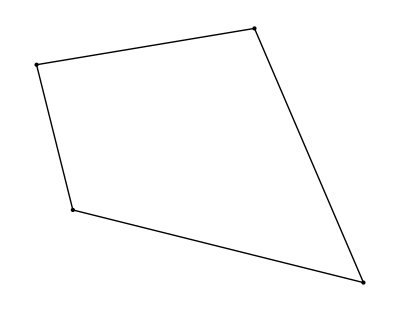

```mathematica
SlikaŠtirikotnik[štirikotnik]
```

{{{-2,1},{7,-5}},{{4,2},{-1,-3}}}

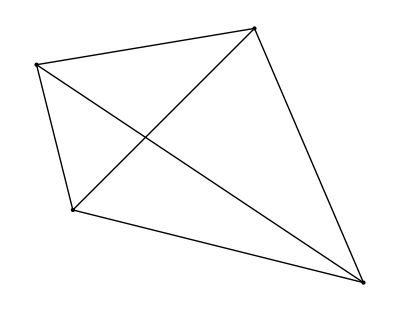

```mathematica
diagonale = {{AA, CC},{BB, DD}}
Graphics[{Map[Point, oglisca], Map[Line,stranice], Map[Line, diagonale]}, AspectRatio->Full]
```

## Učni list - Kombinatorika in verjetnost

5. Na koliko načinov lahko v šolsko puščico po vrsti zložimo osem barvic?

--> uporabila bi formulo za permutacije brez ponavljanja ker predpostavljam da so si vse barvice med seboj različne in ker je vrstni red pomemben, saj me sprašuje na koliko načinov

```mathematica
rezulat = 8!
```

40320

Odgovor: Lahko zložim na 40 320 načinov.

## Učni list - Polinomi - 1

8. Deli in rezultat zapiši v obliki p(x) = k(x)  × q(x) + o(x):
a) (12 x^4 - 30 x^3 - 38 x^2 + 40x + 28) : (6 x^2 - 7) = ?

```mathematica
PolynomialQuotientRemainder[(12 x^4-30 x^3-38 x^2+40x+28), (6 x^2-7), x]
```

{-4-5 x+2 x^2,5 x}

Rešitev :  (12 x^4 - 30 x^3 - 38 x^2 + 40x + 28) =  (6 x^2 - 7) × (-4-5 x+2 x^2) + 5x

b) (6 x^4 -  x^3 - 2x - 6) :  (3 x^3 - 2 x^2 + x -4) = ?

```mathematica
PolynomialQuotientRemainder[(6 x^4-x^3-2x-6), (3 x^3-2 x^2+x-4), x]
```

{1+2 x,-2+5 x}

Rešiev :  (6 x^4 -  x^3 - 2x - 6) =  (3 x^3 - 2 x^2 + x -4) × (1 + 2 x) + -2 + 5x

c) (3 x ^4 - 20 x^3 + 24 x^2 + 11x - 10) : (x^2 - 5x) = ?

```mathematica
PolynomialQuotientRemainder[(3 x^4-20 x^3+24 x^2+11x-10), (x^2-5x), x]
```

{-1-5 x+3 x^2,-10+6 x}

Rešitev : (3 x ^4 - 20 x^3 + 24 x^2 + 11x - 10) = (x^2 - 5x) × (-1-5 x+3 x^2)  - 10 + 6 x

d) (8 x ^5 - 40 x^4 + 28 x^3 - 13 x^2  + 76x - 29) : (2 x^2 - 9x + 3) = ?

```mathematica
PolynomialQuotientRemainder[(8 x^5-40 x^4+28 x^3-13 x^2+76x-29), (2 x^2-9x+3), x]
```

{-8-x-2 x^2+4 x^3,-5+7 x}

Rešitev : (8 x ^5 - 40 x^4 + 28 x^3 - 13 x^2  + 76x - 29) = (2 x^2 - 9x + 3) × (-8-x-2 x^2+4 x^3)  - 5 + 7 x

e) (10 x ^5 - 21 x^4 - 17 x^3 - 17 x^2  - 4 x + 2) : (2 x^3 + 5 x^2 - x + 4) = ?

```mathematica
PolynomialQuotientRemainder[(10 x^5-21 x^4-17 x^3-17 x^2-4 x+2), (2 x^3+5 x^2-x+4),x]
```

{103/2-23 x+5 x^2,-204+(279 x)/2-(635 x^2)/2}

Rešitev : (10 x ^5 - 21 x^4 - 17 x^3 - 17 x^2  - 4 x + 2) = (2 x^3 + 5 x^2 - x + 4) × (103/2-23 x+5 x^2)  -204+(279 x)/2-(635 x^2)/2

## Učni list - Polinomi - 2

13. Izračunaj ničle in nariši graf polinoma:
a) p(x) = x^3 - 4 x^2 + x + 6

```mathematica
Solve[ x^3-4 x^2+x+6 == 0 , x]
```

{{x→-1},{x→2},{x→3}}

Ničle polinoma so: x1 = -1, x2 = 2, x3 = 3.

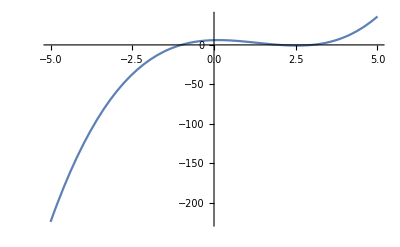

```mathematica
Plot[x^3-4 x^2+x+6, {x, -5, 5}]
```

b) p(x) = 6 x^3 + 7 x^2 - 1

```mathematica
Solve[6 x^3+7 x^2-1 == 0, x]
```

{{x→-1},{x→-1/2},{x→1/3}}

Ničle polinoma so: x1 = -1, x2 = - 1 / 2, x3 = 1 / 3.

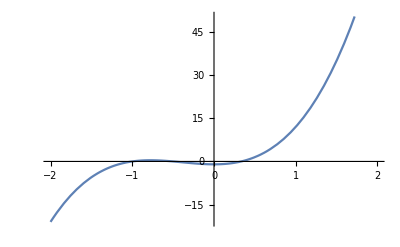

```mathematica
Plot[6 x^3+7 x^2-1 , {x, -2, 2}]
```

c) p(x) = x^3 - 7 x^2 + 15 x - 9

```mathematica
Solve[x^3-7 x^2+15 x-9 == 0, x]
```

{{x→1},{x→3},{x→3}}

Ničle polinoma so: x1 = 1, x2 = 3, x3 = 3.

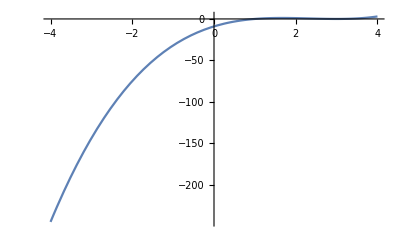

```mathematica
Plot[x^3-7 x^2+15 x-9, {x, -4, 4}]
```

d) p(x) = x^3 - 7 x +  6

```mathematica
Solve[x^3-7 x+6 == 0, x]
```

{{x→-3},{x→1},{x→2}}

Ničle polinoma so: x1 = - 3, x2 = 1, x3 = 2.

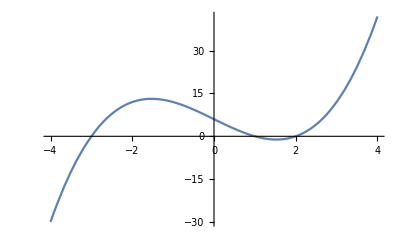

```mathematica
Plot[x^3-7 x+6, {x, -4, 4}]
```

## Učni list - Logaritem - 1

4. Z uporabo definicije logaritma reši naslednje logaritemske enačbe: 
a) log(x)16 = 2

```mathematica
Solve[x ^2 == 16, x]
```

{{x→-4},{x→4}}

Rešitev: x je 4 ali -4.

b) log(x)9 = -(2 / 3)

```mathematica
Solve[x ^(-2/3) == 9, x]
```

{{x→1/27}}

Rešitev: x je 1/27.

c) log(x)16 = 4/3

```mathematica
Solve[x ^(4/3) == 16, x]
```

{{x→8}}

Rešitev: x je 8.

d) log(x)27 = 3/4

```mathematica
Solve[x ^(3/4) == 27, x]
```

{{x→81}}

Rešitev: x je 81.

e) log(x)1.25 = -1

```mathematica
Solve[x ^(-1)== 5 / 4, x]
```

{{x→4/5}}

Rešitev: x je 5 / 4.

f) log(x)0.001 = -3

```mathematica
Solve[x ^(-3) == 1 / 1000]
```

{{x→10},{x→-10 (-1)^(1/3)},{x→10 (-1)^(2/3)}}

Rešitev: x je 10 ali -10 (-1)^(1/3)  ali -10 (-1)^(2/3).

## Učni list - Logaritem - 2

10. Reši enačbe:
a) log(x + 2) + log(x - 3) = log(x - 1) + log(x + 3)

```mathematica
Solve[Log[x + 2] + Log[x - 3] == Log[x  - 1] + Log[x + 3], x]
```

{{x→-1}}

Rešitev: x = - 1.

b) log(x - 2) + log(x + 1) = log(x + 4) + log( x + 3)

```mathematica
Solve[Log[x- 2] + Log[x+1] == Log[x+4] + Log[x+3], x]
```

{}

c) log(x - 5) - log(x - 6) = log(x + 5) - log( x - 1)

```mathematica
Solve[Log[x - 5] - Log[x - 6] == Log[x + 5]- Log[x - 1], x]
```

{{x→7}}

Rešitev: x = 7.

d) log(3x + 2) - log2  = log(x^2 + x + 2) - log( x + 2)

```mathematica
Solve[Log[3x + 2] - Log[2] == Log[x^2 +x + 2] - Log[x + 2], x]
```

{{x→0}}

Rešitev: x = 0.

e) log(3x - 2) - log(x + 3)  -  log(2x + 1) = log( x + 2)

```mathematica
Solve[Log[3x - 2]- Log[x + 3] - Log[2x + 1]== Log[x + 2], x]
```

{{x→1/4 (-3-ⅈ √7)},{x→1/4 (-3+ⅈ √7)}}

Rešitev: x1 = 1/4 (-3-ⅈ √7), x2 = 1/4 (-3+ⅈ √7).

f) log(x - 3) - log(x - 2) =   log(2x - 9) +  log( x + 1)

```mathematica
N@Solve[Log[x - 3] - Log[x - 2]== Log[2x - 9]+ Log[x + 1], x]
```

{{x→4.55478+0. ⅈ},{x→2.06278+2.22045×10^-16 ⅈ}}

Rešitev: x1 = 4.55478+0. ⅈ , x2 = 2.06278+2.22045×10^-16 ⅈ.

## Učni list - Racionalna funkcija

7. Nariši grafe racionalne funkcije: 
a) f(x)  = (3x^2 + 6x - 24)/(x^2 - 2x- 3)

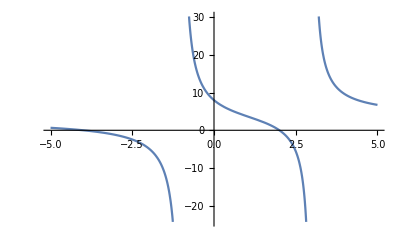

```mathematica
Plot[(3x^2 + 6x - 24)/(x^2 - 2x- 3), {x, -5, 5}]
```

b) f(x)  = (x^2 -7x + 10)/(x^2 - 2x- 8)

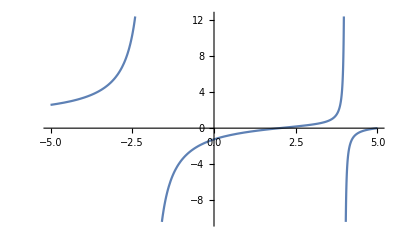

```mathematica
Plot[(x^2 -7x + 10)/(x^2 - 2x- 8), {x, -5, 5}]
```

c) f(x)  = (2x^2 -6x - 8)/(x^2  + x- 6)

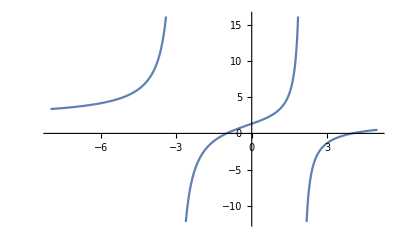

```mathematica
Plot[(2x^2 -6x - 8)/(x^2  + x- 6), {x, -8, 5}]
```

d) f(x)  = (2x - 3)/(x^2  + 4x)

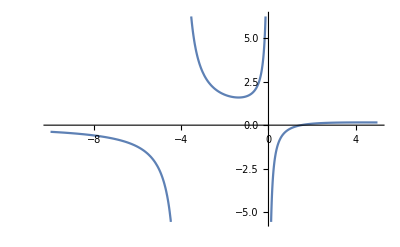

```mathematica
Plot[(2x - 3)/(x^2  + 4x), {x, -10, 5}]
```